```mathematica
$Assumptions={0<u<1};
Q[a_,b_,x_]:=Function[z,FullSimplify[(b-a^2/4-D[a,x]/2)/.x->z]];(*From f''+af'+bf==0 to y''+Qy==0*)
M/.{$θ->0,$g[x]->((1+x)√u)/(1-u),$ϵ[x]->1-(1+x)/(1-u),Subscript[$ϵ, l][x]->-x}//Simplify;
(ⅈ χ%.({{Subscript[Ε, y][x]}, {Subscript[Ε, z][x]}, {Subscript[B, y][x]}, {Subscript[B, z][x]}}));
Assuming[0<a<1&&0<u<1&&-1<ξ<1,Simplify[(D[%⟦2⟧,x]⟦1⟧/.Subscript[B, y]'[x]->%⟦3⟧)⟦1⟧/.Solve[Subscript[Ε, y]'[x]==%⟦1⟧,Subscript[B, z][x]]⟦1⟧/.{Subscript[Ε, y]'[x]->D[ⅈ a(√u ξ+x)A[x],x],Subscript[Ε, z][x]->1}/.Sin[$η]->√((√u)/(1+√u)(*(1+ξ)*))]];
Q[Limit[-%/A'[x],A'[x]->Infinity],Limit[-%/A[x],A[x]->Infinity],x][x];
Normal[Series[%,{x,0,2},{ξ,0,1}]]//Simplify;
Apart[%,x]
```

-(ⅈ a u^(1/4) χ)/(2 √(1+√u))+(ⅈ a x^2 χ)/(2 √(1+√u) u^(3/4))-(ⅈ a x^2 χ)/(2 √(1+√u) u^(1/4))-(ⅈ a u^(1/4) ξ χ)/(2 √(1+√u))+(ⅈ a u^(3/4) ξ χ)/(2 √(1+√u))+(ⅈ a x ξ χ)/(√(1+√u) u^(1/4))-(ⅈ a u^(1/4) x ξ χ)/(√(1+√u))-(3 ⅈ a x^2 ξ χ)/(2 √(1+√u) u^(3/4))+(3 ⅈ a x^2 ξ χ)/(2 √(1+√u) u^(1/4))+(a^2 u x ξ χ^2)/(2 (1+√u))+(a^2 √u x^2 (1-4 ξ+4 √u ξ) χ^2)/(4 (1+√u))

```mathematica
(ⅈ a u^(1/4) χ)/(√(1+√u))-(ⅈ a u^(1/4) x^2 χ)/(√(1+√u))+(ⅈ a u^(3/4) x^2 χ)/(√(1+√u))+(ⅈ a u^(1/4) ϕ χ)/(4 √(1+√u))-(ⅈ a u^(1/4) x ϕ χ)/(√(1+√u))+(ⅈ a u^(3/4) x ϕ χ)/(√(1+√u))+(a^2 u x ϕ χ^2)/(1+√u)+(a^2 u x^2 χ^2)/(1+√u)
```

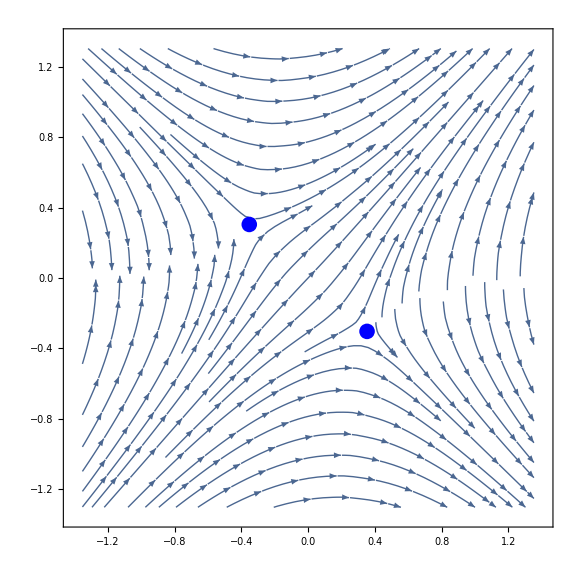
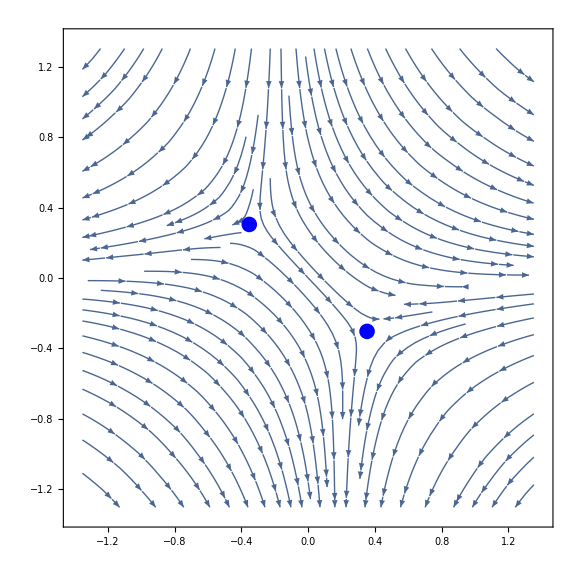

```mathematica
u=0.1;χ=60;
ξ=χ(√u)/(1+√u);ϕ=0;
α=ⅈ ξ(1-√u)-ξ^2 √u;
potential=Function[x,x^2 α+x ϕ α-ⅈ ξ(1+ϕ/4)];
StokesGraph[potential,1]
Clear[u,χ,ξ,ϕ,α,potential];
```

```mathematica
Solve[α x^2+α ϕ x-ⅈ ξ(1+ϕ/4)==0,x]//Simplify
```

{{x→-ϕ/2-(√(α ϕ^2+ⅈ ξ (4+ϕ)))/(2 √α)},{x→(-√α ϕ+√(α ϕ^2+ⅈ ξ (4+ϕ)))/(2 √α)}}

```mathematica
a=-ϕ/2-(√(α ϕ^2+ⅈ ξ (4+ϕ)))/(2 √α);
b=(-√α ϕ+√(α ϕ^2+ⅈ ξ (4+ϕ)))/(2 √α);
c=1/√α;
Clear[a,b,c]
```

{-0.242418+0.234472 ⅈ,0.242418-0.234472 ⅈ}

-1.86722-0.0311118 ⅈ

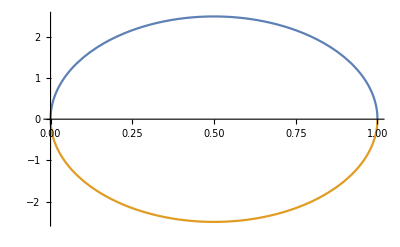
{-Graphics-,-Graphics-}

```mathematica
u=0.5;χ=30;
ξ=χ(√u)/(1+√u);ϕ=0;α=ⅈ ξ(1-√u)-ξ^2 √u;
(*a=-ϕ/2-(√(α ϕ^2+ⅈ ξ (4+ϕ)))/(2 √α);b=(-√α ϕ+√(α ϕ^2+ⅈ ξ (4+ϕ)))/(2 √α);c=1/√α;*)
potential=Function[x,α x^2+α ϕ x-ⅈ ξ(1+ϕ/4)];

zeros=NSolve[potential[z]==0,z];
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

a=zeros⟦2⟧;
b=zeros⟦1⟧;

f=Function[t,potential[line[a,b][t]]];
chunks=sqrt[f,{t,0,10^-10,1-10^-10,1}];
sqrtf=Function[t,chunks];

NIntegrate[-ⅈ (a-b)sqrtf[t],{t,0,1}]
{Plot[{Re[√f[t]],Im[√f[t]]},{t,0,1}],Plot[{Re[sqrtf[t]],Im[sqrtf[t]]},{t,0,1},PlotRange->Full]}

Clear[δ,β,a,b,f,zeros,chunks,sqrtf,potential,u,χ,ξ,ϕ,α];
```

```mathematica
M/.{$θ->0,$g[x]->√u,$ϵ[x]->-x,Subscript[$ϵ, l][x]->-x}//Simplify//MatrixForm
```

(0 | (ⅈ √u Sin[$η])/x | 0 | (x+Sin[$η]^2)/x
0 | 0 | -1 | 0
0 | -u/x+x+Sin[$η]^2 | 0 | (ⅈ √u Sin[$η])/x
-x | 0 | 0 | 0)

```mathematica
$Assumptions={0<u<1};
Q[a_,b_,x_]:=Function[z,FullSimplify[(b-a^2/4-D[a,x]/2)/.x->z]];(*From f''+af'+bf==0 to y''+Qy==0*)
M/.{$η->0,$g[x]->√u,$ϵ[x]->-x,Subscript[$ϵ, l][x]->-x}//Simplify;
(ⅈ χ%.({{0}, {Ε[x]}, {B[x]}, {0}}))⟦{2,3}⟧//Simplify//MatrixForm
D[%⟦2⟧,x]⟦1⟧/.Solve[Ε'[x]==%⟦1⟧,Ε'[x]]⟦1⟧/.Solve[B'[x]==%⟦2⟧,Ε[x]]⟦1⟧//Simplify//Apart
```

(-(ⅈ χ (B[x] (x+Sin[$θ]^2)-ⅈ √u Sin[$θ] Ε[x]))/x
(χ (√u B[x] Sin[$θ]-ⅈ (u-x^2) Ε[x]))/x)

(χ B[x] (u^2 χ-2 u x^2 χ+x^4 χ-2 √u x Sin[$θ]-u x χ Sin[$θ]^2+x^3 χ Sin[$θ]^2))/(x (-u+x^2))+((u+x^2) B'[x])/(x (-u+x^2))

```mathematica
(χ (u^2 χ-2 u x^2 χ+x^4 χ-2 √u x Sin[$θ]-u x χ Sin[$θ]^2+x^3 χ Sin[$θ]^2))/(x (-u+x^2))//Apart
```

((-u+x^2) χ^2)/x+(2 √u χ Sin[$θ])/(u-x^2)+χ^2 Sin[$θ]^2